# Простой нейрон

## https://www.wolframcloud.com/obj/gurgutan/Published/4.3.nb

### Линейный нейрон

```mathematica
ClearAll[w,x,b];
```

```mathematica
Manipulate[Plot[{w*x+b},{x,-8,8},PlotRange->{-4,4}],{w,-4,4},{b,-4,4}]
```

### Линейный нейрон с двумя параметрами

```mathematica
Manipulate[Plot3D[{w1*x1+w2 *x2+b},{x1,-4,4}, {x2,-4,4}, PlotRange->{-8,8}],{w1,-4,4},{w2,-4,4},{b,-4,4}]
```

### Нейрон с нелинейной функцией

```mathematica
f[x_,α_] := 1/(1+Exp[-x*α]);
Manipulate[Plot[f[x,a],{x,-8,8}, PlotRange->{-1,1}],{a,-4,4}]
```

```mathematica
Manipulate[Plot[f[x*w+b,a],{x,-8,8},PlotRange->{-2,2}],{a,-4,4}, {w,-4,4},{b,-4,4}]
```

### Сеть из трех нейронов одним входом и одним выходом

```mathematica
g[x_,w_,b_]:=f[x*w+b,2];
g2[x1_,x2_,w1_,w2_,b_]:=f[w1*x1+w2*x2+b,1];
```

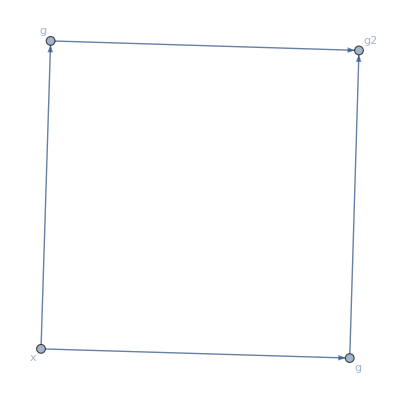
{(0 | 1 | 1 | 0
0 | 0 | 0 | 1
0 | 0 | 0 | 1
0 | 0 | 0 | 0),-Graphics-}

```mathematica
m={{0,1, 1,0},{0,0,0,1},{0,0,0,1},{0,0,0,0}};
{MatrixForm[m],AdjacencyGraph[m,VertexLabels->{1->"x",2->"g",3->"g",4->"g2"}, GraphLayout->"SpringElectricalEmbedding"]}
```

```mathematica
Manipulate[Plot[g2[g[x,w1,b1],g[x,w2,b2],w3,w4,b3],{x,-4,4},PlotRange->{-1,1}],{w1,-4,4}, {w2,-4,4},{w3,-4,4},{w4,-4,4},{b1,-4,4},{b2,-4,4},{b3,-4,4}]
```

### Сеть с двумя входами

Вид функции: f_3(x,y)=w_3 f_1(w_1 x+b_1)+w_4 f_2(w_2 y+b_2)+b

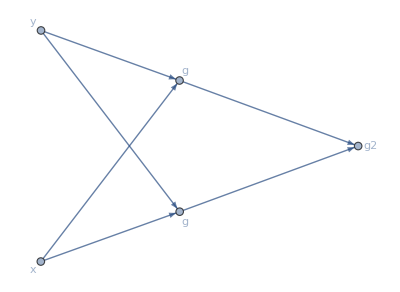

```mathematica
m={{0,0,1, 1,0},{0,0,1,1,0},{0,0,0,0,1},{0,0,0,0,1},{0,0,0,0,0}};
AdjacencyGraph[m,VertexLabels->{1->"x",2->"y",3->"g",4->"g",5->"g2"}, GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
Manipulate[Plot3D[g2[g[x1,w1,b1],g[x2,w2,b2],w3,w4,b3],{x1,-8,8},{x2,-8,8},PlotRange->{{-2,2},{-2,2}}],{w1,-4,4}, {w2,-4,4},{w3,-4,4},{w4,-4,4},{b1,-4,4},{b2,-4,4},{b3,-4,4}]
```